```mathematica
(*Check on β2, which includes both YH and YF*)
```

Setup

```mathematica
(*Check on β2, which includes both YH and YF*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Ratesfunc[x_] :=(
ts=x[[1]];
M=x[[2]];
B0=x[[3]];
Em=x[[4]];
Emprime=x[[5]];
η=x[[6]];
λ0=x[[7]];
γ=x[[8]];
ζ=x[[9]];
f0=x[[10]];
mm0=x[[11]];
alpha=x[[12]];
Ed=x[[13]];
c=x[[14]];
k=x[[15]];
χ=x[[16]];

(*TimeScales*)
a = B0/Em;
aprime =  B0/Emprime;
ϵLam = 0.95;
m0 = (.0558*(1/1000)^.92*M^0.92)*1000;(*0.00001;*)
ϵSig = (1-f0*M^γ/M);
ϵMu = (1-(f0*M^γ+mm0*M^ζ)/M);
τLam = -Log[(1-ϵLam^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
τLamInvade = -Log[(1-(ϵLam*(1+χ))^(1/4))/(1 - (m0/M)^(1/4))]*(4*(M)^(1/4))/a;
τRhoStart = -Log[(1-(ϵSig*ϵLam)^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
(*τRhoStartInvade = -Log[(1-(ϵSig*ϵLam)^(1/4))/(1 - (m0/(M*(1+χ)))^(1/4))]*(4*(M)^(1/4))/a;*)
τRho = -Log[(1-ϵLam^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*M^(1/4))/aprime;
τRhoInvade = -Log[(1-(ϵLam*(1+χ))^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*(M)^(1/4))/aprime;
τSig = -M^(1/4)/aprime*Log[ϵSig];
τSigInvade =  -(M)^(1/4)/aprime*Log[ϵSig/(1+χ)];
τMu = -M^(1/4)/aprime*Log[ϵMu] -τSig;

(*BLam and Brho*)
BLam=1/(3 a)ⅇ^(-(a τLam)/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam)/M^(1/4))) m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4))+ⅇ^((a τLam)/M^(1/4)) (-25+12 (m0/M)^(1/4)+6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam);
BRho=1/(3 a)M^(1/4) (ⅇ^(-(a τLam)/M^(1/4)) (-3 m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam)+ⅇ^(-(a τRhoStart)/M^(1/4)) (3 m0+M (48 ⅇ^((3 a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))+36 ⅇ^((a τRhoStart)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2+16 ⅇ^((a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (1-4 (m0/M)^(1/4)+6 √(m0/M)-4 (m0/M)^(3/4)))-3 a ⅇ^((a τRhoStart)/M^(1/4)) M^(3/4) τRhoStart));
BLamInvade=1/(3 a)ⅇ^(-(a τLamInvade)/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLamInvade)/M^(1/4))) m0+M (-48 ⅇ^((3 a τLamInvade)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLamInvade)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLamInvade)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4))+ⅇ^((a τLamInvade)/M^(1/4)) (-25+12 (m0/M)^(1/4)+6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLamInvade)/M^(1/4)) M^(3/4) τLamInvade);
BRhoInvade=1/(3 a)M^(1/4) (ⅇ^(-(a τLamInvade)/M^(1/4)) (-3 m0+M (-3+12 (m0/M)^(1/4)-2 (9 √(m0/M)-6 (m0/M)^(3/4)+24 ⅇ^((3 a τLamInvade)/(4 M^(1/4))) (-1+(m0/M)^(1/4))+18 ⅇ^((a τLamInvade)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2+8 ⅇ^((a τLamInvade)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3))+3 a ⅇ^((a τLamInvade)/M^(1/4)) M^(3/4) τLamInvade)+ⅇ^(-(a τRhoStart)/M^(1/4)) (3 m0+M (48 ⅇ^((3 a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))+36 ⅇ^((a τRhoStart)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2+16 ⅇ^((a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (1-4 (m0/M)^(1/4)+6 √(m0/M)-4 (m0/M)^(3/4)))-3 a ⅇ^((a τRhoStart)/M^(1/4)) M^(3/4) τRhoStart));

(*Yields for starving and full organisms*)
YF=M*Ed/BLam;
YH=M*Ed/BRho;
YFInvade=M*(1+χ)*Ed/BLamInvade;
YHInvade=M*(1+χ)*Ed/BRhoInvade;
(*Rates*)

ConsumerGrowth = ts*(Log[2]/τLam); (*Fecundity = 2*)
InvaderConsumerGrowth= ts*(Log[2]/τLam); (*Fecundity = 2*)

Starvation = ts*(1/τSig);
InvaderStarvation = ts*(1/τSigInvade);

Mortality=ts*( 1/τMu);

Recovery = ts*(1/τRho);
InvaderRecovery= ts*(1/τRhoInvade);

PF=(B0*M^η)/M/Ed;
(*PH=PF;*)
PH=(B0*(ϵSig*M)^η)/(ϵSig*M)/Ed;

PFInvade=(B0*(M*(1+χ))^η)/(M*(1+χ))/Ed;
(*PHInvade=PFInvade;*)
PHInvade=(B0*(ϵSig*(1+χ)*M)^η)/(ϵSig*(1+χ)*M)/Ed;

StarveMaintenance = ts*PH*(YH/(c/k));
FullMaintenance = ts*((ConsumerGrowth/YF+PF)*(YH/(c/k)));

InvaderStarveMaintenance = ts*PHInvade*(YHInvade/(c/k));
InvaderFullMaintenance = ts*((InvaderConsumerGrowth/YFInvade+PFInvade)*(YHInvade/(c/k)));
(*
StarveMaintenance = ts*((B0*M^η*YH)/(c/k*M*Ed));
FullMaintenance = ts*(YH*(ConsumerGrowth/YF+(B0*M^η))/(c/k));

InvaderStarveMaintenance = ts*((B0*(M*(1+χ))^η*YH)/(c/k*(M*(1+χ))*Ed));
InvaderFullMaintenance = ts*(YH*(ConsumerGrowth/YF+(B0*(M*(1+χ))^η))/(c/k));
*)
ResourceGrowth = ts*alpha;

{ConsumerGrowth,Starvation,Mortality,Recovery,StarveMaintenance,FullMaintenance,ResourceGrowth,InvaderConsumerGrowth,InvaderStarvation,InvaderRecovery,InvaderStarveMaintenance,InvaderFullMaintenance,YH,YF,k,YHInvade}
);
```

```mathematica
parameters={
(*ts*)1,
(*M*)M,
(*B0*)4.7*10^(-2),
(*Em*)5774(*J/gram*),
(*Emprime*)7000 (*10000*),
(*η*)3/4,
(*λ0*)3.39*10^(-7),
(*γ*)1.19,
(*ζ*)1.00,
(*f0*)0.0202,
(*mm0*)0.383,
(*α*)(*2.10*10^(-9)*)(9.45*10^(-9)),
(*Ed*)18200,
(*c*)(*5*)23000,
(*k*)(*10*)23000/2,
(*χ*)chi};
RF =Ratesfunc[parameters];
```

```mathematica
dimSS[ndSS_]:=(
ndSS*YH*k
);
dimSSInvader[ndSS_]:=(
ndSS*YHInvade*k
);
dimRSS[ndR_]:=(
ndR*c
);
```

```mathematica
dF =λ*F-σ*(1-R)*F +ρ*c/k* R * H;
dH =σ*(1-R)*F - ρ*c/k* R*H - μ*H;
dR =α*R*(1-R) -ρ*H*R -δ*H- β*F;
SteadyStateSol = FullSimplify[Solve[
{
0 ==dF,
0==dH,
0 ==dR 
},{F,H,R}]
]
FSS = F/.SteadyStateSol[[3]]
HSS = H/.SteadyStateSol[[3]]
RSS = R/.SteadyStateSol[[3]]
```

{{F→0,H→0,R→0},{F→0,H→0,R→1},{F→-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),H→-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),R→(μ (-λ+σ))/(2 λ ρ+μ σ)}}

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

(μ (-λ+σ))/(2 λ ρ+μ σ)

```mathematica
{{F->0,H->0,R->0},{F->0,H->0,R->1},{F->-((α*λ*μ^2*(μ + 2*ρ)*(λ - σ))/((2*λ*ρ + μ*σ)*(λ*(2*δ*λ + 2*β*μ - λ*μ)*ρ + 
     μ*(β*μ + λ*(δ + ρ))*σ))),H->-((α*λ^2*μ*(μ + 2*ρ)*(λ - σ))/((2*λ*ρ + μ*σ)*(λ*(2*δ*λ + 2*β*μ - λ*μ)*ρ + 
     μ*(β*μ + λ*(δ + ρ))*σ))),R->(μ*(-λ + σ))/(2*λ*ρ + μ*σ)}}
```

{{F→0,H→0,R→0},{F→0,H→0,R→1},{F→-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),H→-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),R→(μ (-λ+σ))/(2 λ ρ+μ σ)}}

SIMULATION

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,δ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ*c/k* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ*c/k* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -ρ*H[t]*R[t] -δ*H[t]- β*F[t],
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
```

```mathematica
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=Starvation,ρ=Recovery,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
F0=-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=(μ (-λ+σ))/(2 λ ρ+μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}]
(*ListPlot[Traj]*)
]
```

{{{0.000243711,6.29724×10^-6,0.99605}},{{0.00023433,7.36598×10^-6,0.995811}},{{0.000211377,6.93781×10^-6,0.995632}},{{0.000182711,6.13798×10^-6,0.995534}},{{0.000155167,5.2373×10^-6,0.995514}},{{0.000132393,4.42304×10^-6,0.99556}},{{0.000115425,3.7753×10^-6,0.995652}},{{0.000103989,3.30602×10^-6,0.995771}},{{0.0000973929,2.99801×10^-6,0.995902}},{{0.0000949941,2.82828×10^-6,0.996034}},{{0.0000963461,2.77862×10^-6,0.996155}},{{0.000101169,2.83727×10^-6,0.996259}},{{0.000109264,2.99792×10^-6,0.996337}},{{0.00012035,3.25697×10^-6,0.996386}},{{0.00013385,3.60701×10^-6,0.9964}},{{0.000148676,4.02938×10^-6,0.996378}},{{0.000163133,4.49707×10^-6,0.996322}},{{0.000175093,4.93418×10^-6,0.996237}},{{0.000182521,5.28775×10^-6,0.996134}},{{0.000184223,5.48628×10^-6,0.996029}},{{0.000180266,5.49921×10^-6,0.995934}},{{0.000171925,5.33915×10^-6,0.995863}},{{0.000161172,5.05673×10^-6,0.995822}},{{0.000149927,4.71607×10^-6,0.995812}},{{0.000139663,4.37454×10^-6,0.99583}},{{0.000131285,4.07245×10^-6,0.99587}},{{0.000125228,3.83255×10^-6,0.995924}},{{0.000121618,3.66445×10^-6,0.995986}},{{0.00012041,3.57017×10^-6,0.996048}},{{0.000121448,3.54727×10^-6,0.996106}},{{0.000124499,3.59074×10^-6,0.996154}},{{0.000129244,3.69369×10^-6,0.996188}},{{0.000135246,3.84647×10^-6,0.996205}},{{0.000141923,4.03544×10^-6,0.996206}},{{0.000148567,4.2423×10^-6,0.99619}},{{0.000154402,4.44457×10^-6,0.99616}},{{0.000158707,4.61744×10^-6,0.996119}},{{0.000160963,4.73911×10^-6,0.996074}},{{0.000160985,4.79487×10^-6,0.996029}},{{0.000158956,4.78115×10^-6,0.995991}},{{0.000155351,4.70682×10^-6,0.995963}},{{0.000150817,4.58731×10^-6,0.995947}},{{0.000146017,4.44468×10^-6,0.995945}},{{0.000141526,4.29812×10^-6,0.995954}},{{0.000137778,4.16405×10^-6,0.995973}},{{0.000135051,4.05605×10^-6,0.995998}},{{0.000133487,3.98246×10^-6,0.996027}},{{0.000133116,3.9362×10^-6,0.996055}},{{0.000133861,3.93271×10^-6,0.996081}},{{0.000135572,3.96877×10^-6,0.996101}},{{0.000138034,4.01808×10^-6,0.996115}},{{0.000140957,4.09726×10^-6,0.996121}},{{0.000144018,4.19152×10^-6,0.996119}},{{0.00014688,4.28203×10^-6,0.996109}},{{0.000149225,4.37038×10^-6,0.996094}},{{0.00015081,4.44248×10^-6,0.996075}},{{0.000151496,4.48268×10^-6,0.996055}},{{0.000151264,4.50936×10^-6,0.996036}},{{0.00015023,4.48516×10^-6,0.99602}},{{0.000148581,4.44873×10^-6,0.996009}},{{0.000146571,4.39502×10^-6,0.996004}},{{0.000144464,4.33196×10^-6,0.996004}},{{0.000142502,4.26767×10^-6,0.996009}},{{0.00014088,4.2093×10^-6,0.996018}},{{0.000139732,4.16234×10^-6,0.99603}},{{0.000139128,4.13047×10^-6,0.996043}},{{0.000139082,4.11549×10^-6,0.996055}},{{0.000139552,4.11738×10^-6,0.996067}},{{0.00014045,4.13465×10^-6,0.996075}},{{0.000141651,4.16433×10^-6,0.99608}},{{0.00014301,4.20251×10^-6,0.996082}},{{0.000144371,4.24461×10^-6,0.99608}},{{0.000145586,4.28586×10^-6,0.996075}},{{0.00014653,4.32179×10^-6,0.996068}},{{0.000147115,4.34874×10^-6,0.996059}},{{0.000147301,4.36427×10^-6,0.99605}},{{0.0001471,4.36745×10^-6,0.996042}},{{0.000146567,4.35898×10^-6,0.996036}},{{0.000145793,4.34084×10^-6,0.996031}},{{0.000144887,4.31598×10^-6,0.996029}},{{0.000143963,4.28782×10^-6,0.99603}},{{0.000143121,4.25978×10^-6,0.996033}},{{0.000142444,4.23485×10^-6,0.996037}},{{0.000141988,4.21537×10^-6,0.996043}},{{0.000141781,4.20289×10^-6,0.996048}},{{0.000141823,4.19811×10^-6,0.996054}},{{0.000142089,4.20085×10^-6,0.996059}},{{0.000142533,4.21023×10^-6,0.996062}},{{0.000143095,4.22473×10^-6,0.996064}},{{0.000143705,4.24244×10^-6,0.996064}},{{0.000144294,4.26119×10^-6,0.996063}},{{0.000144799,4.27889×10^-6,0.99606}},{{0.000145171,4.29366×10^-6,0.996057}},{{0.000145379,4.30412×10^-6,0.996053}},{{0.000145414,4.30944×10^-6,0.996049}},{{0.000145287,4.30945×10^-6,0.996046}},{{0.000145023,4.30458×10^-6,0.996043}},{{0.000144666,4.29579×10^-6,0.996042}},{{0.00014426,4.28434×10^-6,0.996041}},{{0.000143857,4.27181×10^-6,0.996042}},{{0.000143501,4.25968×10^-6,0.996043}},{{0.000143226,4.24924×10^-6,0.996045}},{{0.000143055,4.24144×10^-6,0.996048}},{{0.000142997,4.23691×10^-6,0.99605}},{{0.000143048,4.23583×10^-6,0.996053}},{{0.000143191,4.23798×10^-6,0.996054}},{{0.000143405,4.24288×10^-6,0.996056}},{{0.00014366,4.24976×10^-6,0.996056}},{{0.000143926,4.25772×10^-6,0.996056}},{{0.000144173,4.26582×10^-6,0.996055}},{{0.000144375,4.27316×10^-6,0.996054}},{{0.000144515,4.27902×10^-6,0.996053}},{{0.000144581,4.28285×10^-6,0.996051}},{{0.000144574,4.28442×10^-6,0.996049}},{{0.000144499,4.28375×10^-6,0.996048}},{{0.000144371,4.28107×10^-6,0.996047}},{{0.00014421,4.2769×10^-6,0.996046}},{{0.000144034,4.27181×10^-6,0.996046}},{{0.000143866,4.26643×10^-6,0.996047}},{{0.000143722,4.26139×10^-6,0.996047}},{{0.000143617,4.2572×10^-6,0.996048}},{{0.000143557,4.25424×10^-6,0.996049}},{{0.000143546,4.25271×10^-6,0.996051}},{{0.00014358,4.25267×10^-6,0.996052}},{{0.000143652,4.25399×10^-6,0.996052}},{{0.000143752,4.25641×10^-6,0.996053}},{{0.000143866,4.2596×10^-6,0.996053}},{{0.00014398,4.26313×10^-6,0.996053}},{{0.000144082,4.2666×10^-6,0.996052}},{{0.000144162,4.26961×10^-6,0.996052}},{{0.000144211,4.27186×10^-6,0.996051}},{{0.000144228,4.27315×10^-6,0.99605}},{{0.000144213,4.27342×10^-6,0.99605}},{{0.00014417,4.27277×10^-6,0.996049}},{{0.000144105,4.27128×10^-6,0.996049}},{{0.000144031,4.26923×10^-6,0.996049}},{{0.000143955,4.2669×10^-6,0.996049}},{{0.000143886,4.26462×10^-6,0.996049}},{{0.000143832,4.26261×10^-6,0.996049}},{{0.000143797,4.26107×10^-6,0.99605}},{{0.000143783,4.26014×10^-6,0.99605}},{{0.00014379,4.25985×10^-6,0.996051}},{{0.000143814,4.26016×10^-6,0.996051}},{{0.000143851,4.261×10^-6,0.996051}},{{0.000143896,4.2622×10^-6,0.996051}},{{0.000143944,4.26361×10^-6,0.996051}},{{0.000143988,4.26505×10^-6,0.996051}},{{0.000144025,4.26637×10^-6,0.996051}},{{0.000144051,4.26743×10^-6,0.996051}},{{0.000144063,4.26813×10^-6,0.99605}},{{0.000144063,4.26845×10^-6,0.99605}},{{0.000144051,4.26836×10^-6,0.99605}},{{0.00014403,4.26792×10^-6,0.99605}},{{0.000144002,4.2672×10^-6,0.99605}},{{0.000143971,4.26632×10^-6,0.99605}},{{0.000143941,4.26535×10^-6,0.99605}},{{0.000143915,4.26445×10^-6,0.99605}},{{0.000143896,4.26369×10^-6,0.99605}},{{0.000143885,4.26316×10^-6,0.99605}},{{0.000143883,4.2629×10^-6,0.99605}},{{0.000143891,4.26292×10^-6,0.996051}},{{0.000143905,4.26319×10^-6,0.996051}},{{0.000143925,4.26369×10^-6,0.996051}},{{0.000143946,4.26431×10^-6,0.996051}},{{0.000143967,4.26499×10^-6,0.996051}},{{0.000143986,4.26561×10^-6,0.996051}},{{0.000144,4.26614×10^-6,0.996051}},{{0.000144007,4.26656×10^-6,0.99605}},{{0.000144008,4.26681×10^-6,0.99605}},{{0.000144003,4.26673×10^-6,0.99605}},{{0.000143992,4.26629×10^-6,0.99605}},{{0.000143978,4.266×10^-6,0.99605}},{{0.000143962,4.26623×10^-6,0.99605}},{{0.000143946,4.26606×10^-6,0.99605}},{{0.000143933,4.26536×10^-6,0.99605}},{{0.000143924,4.26415×10^-6,0.99605}},{{0.000143919,4.26353×10^-6,0.99605}},{{0.00014392,4.26384×10^-6,0.99605}},{{0.000143925,4.26423×10^-6,0.99605}},{{0.000143934,4.26451×10^-6,0.996051}},{{0.000143945,4.26453×10^-6,0.996051}},{{0.000143958,4.26485×10^-6,0.996051}},{{0.000143968,4.26524×10^-6,0.99605}},{{0.000143977,4.26559×10^-6,0.99605}},{{0.000143982,4.26582×10^-6,0.99605}},{{0.000143983,4.26595×10^-6,0.99605}},{{0.000143979,4.26594×10^-6,0.99605}},{{0.000143973,4.26582×10^-6,0.99605}},{{0.000143965,4.26559×10^-6,0.99605}},{{0.000143956,4.26531×10^-6,0.99605}},{{0.000143948,4.26504×10^-6,0.99605}},{{0.000143941,4.26478×10^-6,0.99605}},{{0.000143937,4.2646×10^-6,0.99605}},{{0.000143936,4.26451×10^-6,0.99605}},{{0.000143938,4.26452×10^-6,0.99605}},{{0.000143943,4.26461×10^-6,0.99605}},{{0.00014395,4.26479×10^-6,0.99605}},{{0.000143957,4.265×10^-6,0.99605}},{{0.000143963,4.26521×10^-6,0.99605}},{{0.000143968,4.26541×10^-6,0.99605}},{{0.000143971,4.26554×10^-6,0.99605}},{{0.000143971,4.2656×10^-6,0.99605}},{{0.000143969,4.26559×10^-6,0.99605}},{{0.000143965,4.26551×10^-6,0.99605}},{{0.00014396,4.26536×10^-6,0.99605}},{{0.000143955,4.2652×10^-6,0.99605}},{{0.00014395,4.26503×10^-6,0.99605}},{{0.000143946,4.26488×10^-6,0.99605}},{{0.000143944,4.26478×10^-6,0.99605}},{{0.000143944,4.26474×10^-6,0.99605}},{{0.000143946,4.26476×10^-6,0.99605}},{{0.00014395,4.26485×10^-6,0.99605}},{{0.000143954,4.26497×10^-6,0.99605}},{{0.000143959,4.2651×10^-6,0.99605}},{{0.000143964,4.26526×10^-6,0.99605}},{{0.000143969,4.26542×10^-6,0.99605}},{{0.000143971,4.26553×10^-6,0.99605}},{{0.000143974,4.26563×10^-6,0.99605}},{{0.000143974,4.26569×10^-6,0.99605}},{{0.000143973,4.26569×10^-6,0.99605}},{{0.000143971,4.26565×10^-6,0.99605}},{{0.000143967,4.26557×10^-6,0.99605}},{{0.000143962,4.26544×10^-6,0.99605}},{{0.000143957,4.26529×10^-6,0.99605}},{{0.000143952,4.26514×10^-6,0.99605}},{{0.000143948,4.26499×10^-6,0.99605}},{{0.000143944,4.26484×10^-6,0.99605}},{{0.000143941,4.26471×10^-6,0.99605}},{{0.000143939,4.26463×10^-6,0.99605}},{{0.00014394,4.2646×10^-6,0.99605}},{{0.00014394,4.26459×10^-6,0.99605}},{{0.000143943,4.26463×10^-6,0.99605}},{{0.000143947,4.26474×10^-6,0.99605}},{{0.000143951,4.26485×10^-6,0.99605}},{{0.000143956,4.26497×10^-6,0.99605}},{{0.00014396,4.26513×10^-6,0.99605}},{{0.000143965,4.26528×10^-6,0.99605}},{{0.000143968,4.2654×10^-6,0.99605}},{{0.00014397,4.2655×10^-6,0.99605}},{{0.000143971,4.26557×10^-6,0.99605}},{{0.000143971,4.2656×10^-6,0.99605}},{{0.00014397,4.26559×10^-6,0.99605}},{{0.000143968,4.26556×10^-6,0.99605}},{{0.000143965,4.2655×10^-6,0.99605}},{{0.000143962,4.26543×10^-6,0.99605}},{{0.000143959,4.26533×10^-6,0.99605}},{{0.000143955,4.26523×10^-6,0.99605}},{{0.000143952,4.26513×10^-6,0.99605}},{{0.000143949,4.26502×10^-6,0.99605}},{{0.000143947,4.26493×10^-6,0.99605}},{{0.000143946,4.26488×10^-6,0.99605}},{{0.000143945,4.26484×10^-6,0.99605}},{{0.000143945,4.26481×10^-6,0.99605}},{{0.000143945,4.26479×10^-6,0.99605}},{{0.000143946,4.26481×10^-6,0.99605}},{{0.000143948,4.26484×10^-6,0.99605}},{{0.00014395,4.2649×10^-6,0.99605}},{{0.000143952,4.26494×10^-6,0.99605}},{{0.000143954,4.26499×10^-6,0.99605}},{{0.000143955,4.26505×10^-6,0.99605}},{{0.000143957,4.26511×10^-6,0.99605}},{{0.000143959,4.26517×10^-6,0.99605}},{{0.00014396,4.2652×10^-6,0.99605}},{{0.00014396,4.26522×10^-6,0.99605}},{{0.00014396,4.26524×10^-6,0.99605}},{{0.00014396,4.26525×10^-6,0.99605}},{{0.00014396,4.26526×10^-6,0.99605}},{{0.00014396,4.26525×10^-6,0.99605}},{{0.000143959,4.26523×10^-6,0.99605}},{{0.000143958,4.26521×10^-6,0.99605}},{{0.000143957,4.26518×10^-6,0.99605}},{{0.000143956,4.26516×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143955,4.26512×10^-6,0.99605}},{{0.000143955,4.2651×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143954,4.26508×10^-6,0.99605}},{{0.000143954,4.26508×10^-6,0.99605}},{{0.000143954,4.26508×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143955,4.26509×10^-6,0.99605}},{{0.000143955,4.2651×10^-6,0.99605}},{{0.000143955,4.2651×10^-6,0.99605}},{{0.000143955,4.2651×10^-6,0.99605}},{{0.000143956,4.26511×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26514×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26513×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}},{{0.000143956,4.26512×10^-6,0.99605}}}

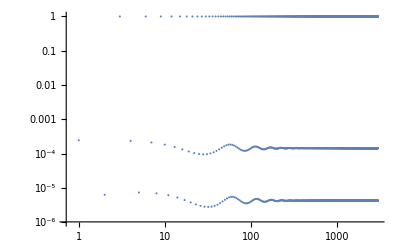

```mathematica
ListLogLogPlot[Flatten[Traj]]
```